### Categorization

Tutorial

SpinorsExtras

SpinorsExtras`

SpinorsExtras/tutorial/QEDWithMuons

### Keywords

Details

# QED with muons

In this tutorial we illustrate how the SpinorsExtras package can be used for calculation of amplitudes including massive spinors and vector bosons on the simple case of QED with photons, electrons and muons. As an example, we calculate the tree level amplitude for e^-μ^-→e^-μ^- scattering using on-shell recursion method. Than we compare it with amplitude calculated using Feynman diagrams and test invariance with respect to change of various reference vectors.

Throughout this tutorial basic familiarity with S@M package is assumed and only functions added in SpinorsExtras package are introduced in definition boxes.

To use SpinorsExtras, one needs to import the package first:

```mathematica
Needs["SpinorsExtras`"]
```

-------  SPINORS @ MATHEMATICA (S@M)  -------


		Version:  S@M 1.0 (3-APR-2007)

 Authors:
	Daniel Maitre (SLAC),
	Pierpaolo Mastrolia (University of Zurich)

A list of all functions provided by the package
is stored in the variable
	$SpinorsFunctions

-------  SpinorsExtras  -------

Version:	1.0.0 (2014.06.18)
Author:	
Documentation:

## On-shell recursion

SpM[p,1] | Labels u spinor for massive momentum p.
PolVec[k,pol] or ϵ^pol(k) | Labels polarization vector for momentum k, and polarization pol.
LightConeDecompose[expr,patt] | Performs light cone decomposition of those massive Lorentz vectors and spinors, in expr, that match patt.
SpRef[k] or q_k | Labels default reference spinor for Lorentz vector k.
SpAssoc[p,q] or p^q | Labels vector associated with massive momentum p by light cone decomposition with (massive or massless) reference vector q.
ExpandPolVec[expr] | Expresses polarization vectors in expr by momentum and reference vectors.
ReplaceLVector[expr,x→y] | Replaces, in expr, Lorentz vectors labeled by x with Lorentz vectors labeled by y.
ReplaceSpinor[expr, x→y] | Replaces, in expr, spinors labeled by x with spinors labeled by y.
ExplicitRef[expr,patt] | Adds explicit reference vectors to all massive spinors, in expr, that match patt.
ShiftBA[p1,p2,z][expr] | For massive Lorentz vectors p1, p2, performes shift described in 
RefSimplify[expr,patt] | Finds simplest form of expr with respect to change of reference vectors matching patt.

Functions used to calculate amplitudes using on-shell recursion.

We start from performing the amplitude calculation using the on-shell recursion technique. It can be done with following steps:

Define basic fermion-vector boson-fermion three point amplitudes:

```mathematica
A[{p1_,+1},{k_,pol_},{p2_,-1}]:=-I Spba[SpM[p2,1],PolVec[k,pol],SpM[p1,1]]

A[{p1_,-1},{k_,pol_},{p2_,+1}]:=-I Spab[SpM[p2,1],PolVec[k,pol],SpM[p1,1]]

A[{p1_,-1},{k_,pol_},{p2_,-1}]:=-I Spbb[SpM[p2,1],PolVec[k,pol],SpM[p1,1]]

A[{p1_,+1},{k_,pol_},{p2_,+1}]:=-I Spaa[SpM[p2,1],PolVec[k,pol],SpM[p1,1]]
```

Declare symbol to be treated as massless labels (k and mk will denote momentum of on-shell photon):

```mathematica
DeclareSpinor[k,mk]
```

{k,mk} added to the list of spinors

Declare symbols to be treated as massive labels (p1, p3 will denote on-shell momenta of massive electrons; p2, p4 momenta of muons; kOff will denote momentum of off-shell photon):

```mathematica
DeclareLVector[p1,p2,p3,p4,kOff]
```

{p1,p2,p3,p4,kOff} added to the list of Lorentz vectors

Assign masses:

```mathematica
MP[p1,p1]^=MP[p3,p3]^=mE^2;
MP[p2,p2]^=MP[p4,p4]^=mMu^2;
$Assumptions=mE>0&&mMu>0;
```

Calculate electron muon scattering diagrams with on-shell photon t-channel exchange.

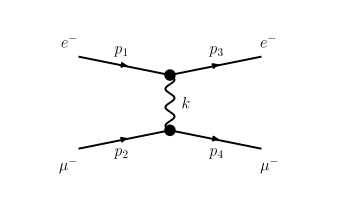

Electrons have positive and muons negative spin projections. Diagram consists of two fermion-vector boson-fermion three point amplitudes connected by photon line. Momentum transfer is denoted by k.

Symbols from S@M package are linear in labels. We a priori don't know whether label representing four-momentum -k will appear in place where it'll be interpreted as object scaling linearly with four-momentum, or as object scaling as square root of four-momentum. In first case it should be labeled by -k and in latter case by ±I k, so we temporarily use mk to represent it.

```mathematica
diags=Table[
A[{p1,1},{k,pol},{p3,1}]
1/s13
A[{p2,-1},{mk,-pol},{p4,-1}]
,
{pol,{-1,1}}
]
```

{(⟨_+p1|ϵ^-(k)|_+p3⟩ [_+p4|ϵ^+(mk)|_+p2])/s13,(⟨_+p1|ϵ^+(k)|_+p3⟩ [_+p4|ϵ^-(mk)|_+p2])/s13}

Decompose spinors for "final" particles:

```mathematica
diagsLCDFinal=LightConeDecompose[diags,p3|p4]//Refine
```

{1/s13(-⟨p3^♭|ϵ^-(k)|_+p1⟩-(mE ⟨_+p1|ϵ^-(k)|q_p3])/[q_p3|p3^♭]) (-(mMu ⟨q_p4|ϵ^+(mk)|_+p2])/⟨p4^♭|q_p4⟩-[_+p2|ϵ^+(mk)|p4^♭]),1/s13(-⟨p3^♭|ϵ^+(k)|_+p1⟩-(mE ⟨_+p1|ϵ^+(k)|q_p3])/[q_p3|p3^♭]) (-(mMu ⟨q_p4|ϵ^-(mk)|_+p2])/⟨p4^♭|q_p4⟩-[_+p2|ϵ^-(mk)|p4^♭])}

Express polarization vectors by momentum and reference vectors:

```mathematica
diagsExpanded=diagsLCDFinal//ExpandPolVec
```

{1/s13(-(√2 ⟨mk|_+p2] [q_mk|p4^♭])/[q_mk|mk]+(√2 mMu ⟨mk|q_p4⟩ [q_mk|_+p2])/(⟨p4^♭|q_p4⟩ [q_mk|mk])) ((√2 ⟨p3^♭|q_k⟩ ⟨_+p1|k])/⟨k|q_k⟩-(√2 mE ⟨_+p1|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 ⟨q_mk|_+p2] [p4^♭|mk])/⟨mk|q_mk⟩+(√2 mMu ⟨q_mk|q_p4⟩ [_+p2|mk])/(⟨mk|q_mk⟩ ⟨p4^♭|q_p4⟩)) ((√2 ⟨k|p3^♭⟩ ⟨_+p1|q_k])/[q_k|k]-(√2 mE ⟨k|_+p1⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

Lorentz vectors labeled by mk can now be replaced with -k and spinors labeled by mk can be replaced with ±I k (in this simple example there are actually no Lorentz vectors mk only spinors):

```mathematica
ReplaceLVector[diagsExpanded,mk->-k];
diagskOnly=ReplaceSpinor[%,mk->±I k]
```

{1/s13(-(√2 ⟨k|_+p2] [q_mk|p4^♭])/[q_mk|k]+(√2 mMu ⟨k|q_p4⟩ [q_mk|_+p2])/(⟨p4^♭|q_p4⟩ [q_mk|k])) ((√2 ⟨p3^♭|q_k⟩ ⟨_+p1|k])/⟨k|q_k⟩-(√2 mE ⟨_+p1|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 ⟨q_mk|_+p2] [p4^♭|k])/⟨k|q_mk⟩+(√2 mMu ⟨q_mk|q_p4⟩ [_+p2|k])/(⟨k|q_mk⟩ ⟨p4^♭|q_p4⟩)) ((√2 ⟨k|p3^♭⟩ ⟨_+p1|q_k])/[q_k|k]-(√2 mE ⟨k|_+p1⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

Add explicit reference vectors to massive spinors that we intend to shift:

```mathematica
diagsExplRef=ExplicitRef[diagskOnly,p1|p2]
```

{1/s13(-(√2 ⟨k|_+^q_p2 p2] [q_mk|p4^♭])/[q_mk|k]+(√2 mMu ⟨k|q_p4⟩ [q_mk|_+^q_p2 p2])/(⟨p4^♭|q_p4⟩ [q_mk|k])) ((√2 ⟨p3^♭|q_k⟩ ⟨_+^q_p1 p1|k])/⟨k|q_k⟩-(√2 mE ⟨_+^q_p1 p1|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 ⟨q_mk|_+^q_p2 p2] [p4^♭|k])/⟨k|q_mk⟩+(√2 mMu ⟨q_mk|q_p4⟩ [_+^q_p2 p2|k])/(⟨k|q_mk⟩ ⟨p4^♭|q_p4⟩)) ((√2 ⟨k|p3^♭⟩ ⟨_+^q_p1 p1|q_k])/[q_k|k]-(√2 mE ⟨k|_+^q_p1 p1⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

Replace default reference vectors with reference vectors for which boundary term, for further shift, will vanish:

```mathematica
diagsProperRef=diagsExplRef/.{SpRef[p1]->SpAssoc[p2,p1],SpRef[p2]->SpAssoc[p1,p2]}
```

{1/s13(-(√2 ⟨k|_+^(p1^p2)p2] [q_mk|p4^♭])/[q_mk|k]+(√2 mMu ⟨k|q_p4⟩ [q_mk|_+^(p1^p2)p2])/(⟨p4^♭|q_p4⟩ [q_mk|k])) ((√2 ⟨p3^♭|q_k⟩ ⟨_+^(p2^p1)p1|k])/⟨k|q_k⟩-(√2 mE ⟨_+^(p2^p1)p1|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 ⟨q_mk|_+^(p1^p2)p2] [p4^♭|k])/⟨k|q_mk⟩+(√2 mMu ⟨q_mk|q_p4⟩ [_+^(p1^p2)p2|k])/(⟨k|q_mk⟩ ⟨p4^♭|q_p4⟩)) ((√2 ⟨k|p3^♭⟩ ⟨_+^(p2^p1)p1|q_k])/[q_k|k]-(√2 mE ⟨k|_+^(p2^p1)p1⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

Find z that will put shifted momentum transfer on-shell:

```mathematica
ShiftBA[p1,p2,z][MP2[p1+p3]==0]
zSol=Solve[%,z]//Flatten
```

2 mE^2+2 (MP[p1,p3]-1/2 z ⟨p1^p2|p3|p2^p1])==0

{z→(2 (mE^2+MP[p1,p3]))/(⟨p1^p2|p3|p2^p1])}

Perform holomorphic shift of p1 and p2 in diagrams (in this simplified example there is actually nothing to shift except momentum transfer which we'll consider separately) and insert proper z:

```mathematica
diagsShifted=diagsProperRef//ShiftBA[p1,p2,z]/.zSol
```

{1/s13(-(√2 ⟨k|_+^(p1^p2)p2] [q_mk|p4^♭])/[q_mk|k]+(√2 mMu ⟨k|q_p4⟩ [q_mk|_+^(p1^p2)p2])/(⟨p4^♭|q_p4⟩ [q_mk|k])) ((√2 ⟨p3^♭|q_k⟩ ⟨_+^(p2^p1)p1|k])/⟨k|q_k⟩-(√2 mE ⟨_+^(p2^p1)p1|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 ⟨q_mk|_+^(p1^p2)p2] [p4^♭|k])/⟨k|q_mk⟩+(√2 mMu ⟨q_mk|q_p4⟩ [_+^(p1^p2)p2|k])/(⟨k|q_mk⟩ ⟨p4^♭|q_p4⟩)) ((√2 ⟨k|p3^♭⟩ ⟨_+^(p2^p1)p1|q_k])/[q_k|k]-(√2 mE ⟨k|_+^(p2^p1)p1⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

After shift we can decompose remaining massive spinors:

```mathematica
diagsShifted//LightConeDecompose//Refine;
diagsLCDAll=%/.{SpAssoc[p1,SpAssoc[p2,p1]]->SpAssoc[p1,p2],SpAssoc[p2,SpAssoc[p1,p2]]->SpAssoc[p2,p1]}
```

{1/s13((√2 mMu ⟨k|p1^p2⟩ [q_mk|p4^♭])/(⟨p1^p2|p2^p1⟩ [q_mk|k])+(√2 mMu ⟨k|q_p4⟩ [q_mk|p2^p1])/(⟨p4^♭|q_p4⟩ [q_mk|k])) ((√2 mE ⟨p3^♭|q_k⟩ [p2^p1|k])/(⟨k|q_k⟩ [p2^p1|p1^p2])-(√2 mE ⟨p1^p2|q_k⟩ [q_p3|k])/(⟨k|q_k⟩ [q_p3|p3^♭])),1/s13(-(√2 mMu ⟨p1^p2|q_mk⟩ [p4^♭|k])/(⟨k|q_mk⟩ ⟨p1^p2|p2^p1⟩)+(√2 mMu ⟨q_mk|q_p4⟩ [p2^p1|k])/(⟨k|q_mk⟩ ⟨p4^♭|q_p4⟩)) (-(√2 mE ⟨k|p3^♭⟩ [q_k|p2^p1])/([p2^p1|p1^p2] [q_k|k])-(√2 mE ⟨k|p1^p2⟩ [q_p3|q_k])/([q_k|k] [q_p3|p3^♭]))}

Spinors related to shifted, on-shell momentum transfer are proportional to slashed off-shell momentum transfer acting on proper spinors related to complexification vector (normalization factor can be added to any spinor):

```mathematica
kB=kOff[SpAssoc[p1,p2]]
kA=kOff[SpAssoc[p2,p1]]/Spba[SpAssoc[p2,p1], kOff, SpAssoc[p1,p2]]
```

kOff[p1^p2]

kOff[p2^p1]/(⟨p1^p2|kOff|p2^p1])

Express photons momentum by external momenta:

```mathematica
ReplaceSpinor[diagsLCDAll,k->{kB,kA}]//UnCompact;
ReplaceLVector[%,kOff->p1-p3];
LightConeDecompose[%,{p1->p2,p3}];
diagsExtern=%/.s13->s[p1,p3]//Simplify
```

{(2 mE mMu (2 MP[p3^♭,q_p3] (⟨p4^♭|q_p4⟩ ⟨p1^p2|p3^♭|p2^p1] [q_mk|p4^♭]+⟨p1^p2|p2^p1⟩ (⟨q_p4|p3^♭|p2^p1]-⟨q_p4|p1^p2|p2^p1]) [q_mk|p2^p1])+mE^2 (⟨p4^♭|q_p4⟩ ⟨p1^p2|q_p3|p2^p1] [q_mk|p4^♭]+⟨p1^p2|p2^p1⟩ ⟨q_p4|q_p3|p2^p1] [q_mk|p2^p1])) (mE^2 MP[p1^p2,p2^p1] ⟨p3^♭|q_k⟩ ⟨p1^p2|q_p3|p2^p1] [q_p3|p3^♭]+MP[p3^♭,q_p3] (mE^2 ⟨p1^p2|q_k⟩ ⟨p1^p2|p2^p1|q_p3] [p2^p1|p1^p2]+MP[p1^p2,p2^p1] (-2 ⟨p1^p2|q_k⟩ ⟨p1^p2|p3^♭|q_p3] [p2^p1|p1^p2]+2 ⟨p3^♭|q_k⟩ ⟨p1^p2|p3^♭|p2^p1] [q_p3|p3^♭]))))/(s_p1p3 ⟨p4^♭|q_p4⟩ ⟨p1^p2|p2^p1⟩ (MP[p3^♭,q_p3] (2 MP[p1^p2,p2^p1] ⟨p1^p2|p3^♭|q_mk]-mE^2 ⟨p1^p2|p2^p1|q_mk])+mE^2 MP[p1^p2,p2^p1] ⟨p1^p2|q_p3|q_mk]) (2 MP[p3^♭,q_p3] (⟨q_k|p3^♭|p2^p1]-⟨q_k|p1^p2|p2^p1])+mE^2 ⟨q_k|q_p3|p2^p1]) [p2^p1|p1^p2] [q_p3|p3^♭]),-(2 mE mMu (MP[p3^♭,q_p3] (MP[p1^p2,p2^p1] (-2 ⟨p4^♭|q_p4⟩ ⟨p1^p2|q_mk⟩ ⟨p1^p2|p3^♭|p4^♭]+2 ⟨p1^p2|p2^p1⟩ ⟨q_mk|q_p4⟩ ⟨p1^p2|p3^♭|p2^p1])+mE^2 ⟨p4^♭|q_p4⟩ ⟨p1^p2|q_mk⟩ ⟨p1^p2|p2^p1|p4^♭])+mE^2 MP[p1^p2,p2^p1] (-⟨p4^♭|q_p4⟩ ⟨p1^p2|q_mk⟩ ⟨p1^p2|q_p3|p4^♭]+⟨p1^p2|p2^p1⟩ ⟨q_mk|q_p4⟩ ⟨p1^p2|q_p3|p2^p1])) (MP[p3^♭,q_p3] (-2 ⟨p3^♭|p1^p2|p2^p1] [q_k|p2^p1] [q_p3|p3^♭]+2 ⟨p1^p2|p3^♭|p2^p1] [p2^p1|p1^p2] [q_p3|q_k])+mE^2 (⟨p3^♭|q_p3|p2^p1] [q_k|p2^p1] [q_p3|p3^♭]+⟨p1^p2|q_p3|p2^p1] [p2^p1|p1^p2] [q_p3|q_k])))/(s_p1p3 ⟨p4^♭|q_p4⟩ ⟨p1^p2|p2^p1⟩ (MP[p3^♭,q_p3] (2 MP[p1^p2,p2^p1] ⟨p1^p2|p3^♭|q_k]-mE^2 ⟨p1^p2|p2^p1|q_k])+mE^2 MP[p1^p2,p2^p1] ⟨p1^p2|q_p3|q_k]) (2 MP[p3^♭,q_p3] (⟨q_mk|p3^♭|p2^p1]-⟨q_mk|p1^p2|p2^p1])+mE^2 ⟨q_mk|q_p3|p2^p1]) [p2^p1|p1^p2] [q_p3|p3^♭])}

Find simplest form of diagrams with respect to reference vectors of exchanged photon (this may take some time).

Note that since each diagram is gauge invariant we can simplify diagrams separately, so we map RefSimplify on list of diagrams:

```mathematica
diagsSimpl=RefSimplify[#,SpRef[k|mk]]&/@diagsExtern
```

{(2 mE mMu ⟨p3^♭|p1^p2⟩ [p2^p1|p4^♭])/(s_p1p3 ⟨p1^p2|p2^p1⟩ [p2^p1|p1^p2]),-(2 mE mMu ⟨p1^p2|q_p4⟩ [q_p3|p2^p1])/(s_p1p3 ⟨p4^♭|q_p4⟩ [q_p3|p3^♭])}

Sum diagrams :

```mathematica
ampl[1,-1,1,-1]=diagsSimpl//Total//Simplify
```

(2 mE mMu ((⟨p3^♭|p1^p2⟩ [p2^p1|p4^♭])/(⟨p1^p2|p2^p1⟩ [p2^p1|p1^p2])-(⟨p1^p2|q_p4⟩ [q_p3|p2^p1])/(⟨p4^♭|q_p4⟩ [q_p3|p3^♭])))/s_p1p3

## Numerical results and comparison with standard amplitude

As we illustrate below SpinorsExtras package can be also used to calculate numerical values of scattering amplitudes. They can be used e.g. for testing the final result by comparing it with amplitude obtained using ordinary Feynman diagrams.

Assign numerical values to masses:

```mathematica
N[mE]=.5;
N[mMu]=105.;
```

Generate random numerical momenta for external particles (such that p1+p2=p3+p4):

```mathematica
SeedRandom[0];
Module[
{
v1=RandomReal[{-100,100},3],
v2=RandomReal[{-100,100},3],
v1Sq,v2Sq,
eE,eMu
}
,

{v1Sq,v2Sq}=Total[#^2]&/@{v1,v2};
v2=√(v1Sq/v2Sq)v2;
{eE,eMu}=√(v1Sq+N[#]^2)&/@{mE,mMu};

DeclareLVectorMomentum[p1,Flatten[{eE,v1}]];
DeclareLVectorMomentum[p2,Flatten[{eMu,-v1}]];
DeclareLVectorMomentum[p3,Flatten[{eE,v2}]];
DeclareLVectorMomentum[p4,Flatten[{eMu,-v2}]];
]
```

Four Momentum p1 set to {54.5458,30.4936,26.6141,36.5626}.

Four Momentum p2 set to {118.322,-30.4936,-26.6141,-36.5626}.

Four Momentum p3 set to {54.5458,5.58062,36.6033,40.0505}.

Four Momentum p4 set to {118.322,-5.58062,-36.6033,-40.0505}.

Assign default numerical values to reference vectors for "final" particles:

```mathematica
DeclareSpinorMomentum/@SpRef/@{p3,p4};
```

Momentum for spinor q_p3 set to {54.5435,-5.58062,-36.6033,-40.0505}.

Momentum for spinor q_p4 set to {54.5435,5.58062,36.6033,40.0505}.

Assign numerical values to associated vectors:

```mathematica
DeclareSpinorMomentum/@{SpAssoc[p1,p2],SpAssoc[p2,p1],SpAssoc[p3],SpAssoc[p4]};
```

Momentum for spinor p1^p2 set to {54.5446,30.4942,26.6146,36.5634}.

Momentum for spinor p2^p1 set to {86.4325,-48.3217,-42.1741,-57.9391}.

Momentum for spinor p3^♭ set to {54.5446,5.58074,36.6041,40.0513}.

Momentum for spinor p4^♭ set to {86.4325,-8.84335,-58.0036,-63.4662}.

### Comparison with standard amplitude

Calculate electron muon scattering amplitude using ordinary Feynman diagrams (there is just one diagram: with off-shell photon t-channel exchange):

```mathematica
GammaVec={Gamma0,Gamma1, Gamma2, Gamma3};
```

```mathematica
1/s13 MP[I Spaa[SpM[p3,1],#,SpM[p1,1]]&/@GammaVec,I Spbb[SpM[p4,1],#,SpM[p2,1]]&/@GammaVec];
LightConeDecompose[%,{p1->p2,p2->p1,p3,p4}]//Refine;
amplStandard=%/.s13->s[p1,p3];
%//N
```

-0.0166026-0.00590979 ⅈ

Compute numerical value of amplitude calculated using on-shell recursion and compare it with amplitude calculated using Feynman diagrams:

```mathematica
ampl[1,-1,1,-1]//N
%==amplStandard//N
```

-0.0166026-0.00590979 ⅈ

True

### Reference vectors independence

DeclareSpinorRandomMomentum[x] | Generates random numerics for x spinor.
RefInvariantQ[expr,q] | Checks whether expr is invariant with respect to change of reference vector q.

Functions used to test numerical invariance of amplitude.

Independence of the final results on the choice of reference vectors can be used as additional test of the correctness of the final result:

Assign random numerical values to reference vectors for exchanged photon:

```mathematica
DeclareSpinorRandomMomentum/@SpRef/@{k,mk};
```

Momentum for spinor q_k set to {0.992881,-0.523097,0.275125,-0.797803}.

Momentum for spinor q_mk set to {0.970702,0.291049,-0.680956,0.627576}.

Set accuracy of numerical invariance tests:

```mathematica
SetOptions[RefInvariantQ,"Accuracy"->15];
```

Test invariance of diagrams with respect to change of reference vectors of on-shell photon:

```mathematica
RefInvariantQ[diagsExtern,SpRef[k]]
RefInvariantQ[diagsExtern,SpRef[mk]]
```

True

True

Test invariance of amplitude with respect to change of reference vectors of external final particles (since different reference vectors correspond to different, distinguishable states, amplitude is not invariant). Invariance testing function needs to take into account all occurrences of reference vector, so we make all occurrences explicit.

```mathematica
RefInvariantQ[ExplicitRef[ampl[1,-1,1,-1],p3],SpRef[p3]]
RefInvariantQ[ExplicitRef[ampl[1,-1,1,-1],p4],SpRef[p4]]
```

False

False

Calculate amplitudes with changed spin projections of final particles:

```mathematica
Table[
Table[
A[{p1,1},{k,pol},{p3,finalSpins//First}] 1/s13 A[{p2,-1},{mk,-pol},{p4,finalSpins//Last}],
{pol,{-1,1}}
],
{finalSpins,{{-1,-1},{1,1}}}
];
LightConeDecompose[%,p3|p4]//Refine//ExpandPolVec;
ReplaceSpinor[%,mk->±I k]//ShiftBA[p1,p2,z]/.zSol;
LightConeDecompose[%,{p1->p2,p2->p1}]//Refine;
ReplaceSpinor[%,k->{kB,kA}]//UnCompact;
ReplaceLVector[%,kOff->p1-p3];
LightConeDecompose[%,{p1->p2,p3}]//Refine;
%/.s13->s[p1,p3]//Simplify;
RefSimplify[#,SpRef[k|mk]]&/@%;
{ampl[1,-1,-1,-1],ampl[1,-1,1,1]}=Total/@%//Simplify
```

{(2 mMu ((⟨p1^p2|q_p4⟩ [p2^p1|p3^♭])/⟨p4^♭|q_p4⟩+(mE^2 ⟨p1^p2|q_p3⟩ [p2^p1|p4^♭])/(⟨p3^♭|q_p3⟩ ⟨p1^p2|p2^p1⟩ [p2^p1|p1^p2])))/s_p1p3,(2 mE (-(⟨p4^♭|p1^p2⟩ [q_p3|p2^p1])/[q_p3|p3^♭]-(mMu^2 ⟨p3^♭|p1^p2⟩ [q_p4|p2^p1])/(⟨p1^p2|p2^p1⟩ [p2^p1|p1^p2] [q_p4|p4^♭])))/s_p1p3}

Square of absolute value of amplitude summed over spin projections of given particle should be independent of reference vector related to this particle:

```mathematica
RefInvariantQ[ExplicitRef[Abs[ampl[1,-1,1,-1]]^2+Abs[ampl[1,-1,-1,-1]]^2,p3],SpRef[p3]]
RefInvariantQ[ExplicitRef[Abs[ampl[1,-1,1,-1]]^2+Abs[ampl[1,-1,1,1]]^2,p4],SpRef[p4]]
```

True

True

More About

SpinorsExtras

Related Tutorials

Related Wolfram Education Group Courses